```mathematica
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],Next,Cell]]
```

```mathematica
$Assumptions={ℏ>0, Subscript[m, n]>0,Subscript[m, s]>0,Subscript[k, x]>0,Subscript[k, y]>0,Subscript[μ, n]≥0, Subscript[μ, s]≥0,α≥0,Ez≥0,θ≥0, q∈Reals,W∈Reals, Subscript[k, 1]∈Reals, Subscript[k, 2]∈Reals,Subscript[ν, arg]∈Reals,ϕ∈Reals};
```

```mathematica
Unprotect[Conjugate];
Conjugate/:MakeBoxes[Conjugate[x_],StandardForm]:=TemplateBox[{Parenthesize[x,StandardForm,Power]},"Conjugate",DisplayFunction->(SuperscriptBox[#1,"*"]&)]
Protect[Conjugate];
```

```mathematica
Subscript[m,n]:=Subscript[m,s]
```

# System description

### Normal

```mathematica
Subscript[H, n]=(ℏ^2/(2*Subscript[m, n])*(Subscript[k, x]^2+Subscript[k, y]^2 )- Subscript[μ, n])*PauliMatrix[0] - α*Subscript[k, x]*PauliMatrix[2] + Ez*(Cos[θ]*PauliMatrix[1] + Sin[θ]*PauliMatrix[2]);
Subscript[H, n]//MatrixForm
```

((ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_n | Ez (Cos[θ]-ⅈ Sin[θ])+ⅈ α k_x
Ez (Cos[θ]+ⅈ Sin[θ])-ⅈ α k_x | (ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_n)

### Superconductor without superconductivity

```mathematica
Subscript[H, s]=(ℏ^2/(2*Subscript[m, s])*(Subscript[k, x]^2+Subscript[k, y]^2) - Subscript[μ, s])*PauliMatrix[0];
Subscript[H, s]//MatrixForm
```

((ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_s | 0
0 | (ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_s)

# Scattering matrix basis

-Graphics-

```mathematica
Subscript[S, sns]=ArrayFlatten[{ {{{Subscript[r, 11,L], Subscript[r, 21,L]},{Subscript[r, 12,L], Subscript[r, 22,L]}}, {{Subscript[t, 11,R], Subscript[t, 21,R]},{Subscript[t, 12,R], Subscript[t, 22,R]}}},
                            {{{Subscript[t, 11,L], Subscript[t, 21,L]},{Subscript[t, 12,L], Subscript[t, 22,L]}}, {{Subscript[r, 11,R], Subscript[r, 21,R]},{Subscript[r, 12,R], Subscript[r, 22,R]}}} }];Subscript[S, sns]//MatrixForm
```

(r_(11,L) | r_(21,L) | t_(11,R) | t_(21,R)
r_(12,L) | r_(22,L) | t_(12,R) | t_(22,R)
t_(11,L) | t_(21,L) | r_(11,R) | r_(21,R)
t_(12,L) | t_(22,L) | r_(12,R) | r_(22,R))

# General Solution

## Energies

### Normal region

```mathematica
Simplify[Eigenvalues[Subscript[H, n]]]//MatrixForm
```

((ℏ^2 k_x^2+ℏ^2 k_y^2-2 m_s (√(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2)+μ_n))/(2 m_s)
(ℏ^2 k_x^2+ℏ^2 k_y^2+2 m_s (√(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2)-μ_n))/(2 m_s))

```mathematica
Subscript[ϵ, 1,n]=(ℏ^2/(2*Subscript[m, n])*(Subscript[k, x]^2+Subscript[k, y]^2)-Subscript[μ, n])+Sqrt[Ez^2-2*Ez*α*Sin[θ]*Subscript[k, x]+α^2*Subscript[k, x]^2]
```

√(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2)+(ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_n

```mathematica
Simplify[Eigenvalues[Subscript[H, n]][[2]]-Subscript[ϵ, 1,n]]
```

0

```mathematica
Subscript[ϵ, 2,n]=(ℏ^2/(2*Subscript[m, n])*(Subscript[k, x]^2+Subscript[k, y]^2)-Subscript[μ, n])-Sqrt[Ez^2-2*Ez*α*Sin[θ]*Subscript[k, x]+α^2*Subscript[k, x]^2]
```

-√(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2)+(ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_n

```mathematica
Simplify[Eigenvalues[Subscript[H, n]][[1]]-Subscript[ϵ, 2,n]]
```

0

```mathematica
subK1=(Solve[Subscript[ϵ, 1,n]==0,Subscript[k, y]][[2]]/.(Subscript[k, y]->Subscript[k, 1]))[[1]]
```

k_1→(√(-ℏ^2 k_x^2-2 √(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2) m_s+2 m_s μ_n))/ℏ

```mathematica
subK2=(Solve[Subscript[ϵ, 2,n]==0,Subscript[k, y]][[2]]/.(Subscript[k, y]->Subscript[k, 2]))[[1]]
```

k_2→(√(-ℏ^2 k_x^2+2 √(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2) m_s+2 m_s μ_n))/ℏ

```mathematica
Simplify[Subscript[ϵ, 1,n]/.(Subscript[k, y]->Subscript[k, 1])/.subK1]
```

0

```mathematica
Simplify[Subscript[ϵ, 2,n]/.(Subscript[k, y]->Subscript[k, 2])/.subK2]
```

0

### Superconducting region

```mathematica
Simplify[Eigenvalues[Subscript[H, s]]]//MatrixForm
```

((ℏ^2 k_x^2+ℏ^2 k_y^2-2 m_s μ_s)/(2 m_s)
(ℏ^2 k_x^2+ℏ^2 k_y^2-2 m_s μ_s)/(2 m_s))

```mathematica
Subscript[ϵ, s]=(ℏ^2/(2*Subscript[m, s])*(Subscript[k, x]^2+Subscript[k, y]^2)-Subscript[μ, s])
```

(ℏ^2 (k_x^2+k_y^2))/(2 m_s)-μ_s

```mathematica
Simplify[Subscript[ϵ, s]-Eigenvalues[Subscript[H, s]][[1]]]
```

0

```mathematica
subQ=(Solve[Subscript[ϵ, s]==0,Subscript[k, y]][[2]]/.(Subscript[k, y]->q))[[1]]
```

q→(√(-ℏ^2 k_x^2+2 m_s μ_s))/ℏ

```mathematica
Simplify[Subscript[ϵ, s]/.(Subscript[k, y]->q)/.subQ]
```

0

## Spinors

### Normal region

```mathematica
Simplify[Eigenvectors[Subscript[H, n]]]//MatrixForm
```

(-(ⅈ √(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2))/(ⅈ Ez Cos[θ]-Ez Sin[θ]+α k_x) | 1
(√(Ez^2-2 Ez α Sin[θ] k_x+α^2 k_x^2))/(Ez (Cos[θ]+ⅈ Sin[θ])-ⅈ α k_x) | 1)

```mathematica
Subscript[Ψ, n,1]={1,Exp[I*Subscript[ν, arg]]};Subscript[Ψ, n,1]//MatrixForm
```

(1
ⅇ^(ⅈ ν_arg))

```mathematica
Subscript[Ψ, n,2]={1,-Exp[I*Subscript[ν, arg]]};Subscript[Ψ, n,2]//MatrixForm
```

(1
-ⅇ^(ⅈ ν_arg))

```mathematica
nuArg=Subscript[ν, arg]->I*Log[Sqrt[((Ez*(Cos[θ]+ⅈ Sin[θ])-ⅈ α Subscript[k, x]) * (Ez*(Cos[θ]-ⅈ Sin[θ])+ⅈ α Subscript[k, x]))]/(Ez*(Cos[θ]+ⅈ Sin[θ])-ⅈ α Subscript[k, x])];
```

```mathematica
Subscript[N, 1]=Sqrt[Subscript[v, 1]]
```

√v_1

```mathematica
Subscript[N, 2]=Sqrt[Subscript[v, 2]]
```

√v_2

### Superconducting region

```mathematica
Simplify[Eigenvectors[Subscript[H, s]]]//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
Subscript[Ψ, s,1]={1,0};Subscript[Ψ, s,1]//MatrixForm
```

(1
0)

```mathematica
Subscript[Ψ, s,2]={0,1};Subscript[Ψ, s,2]//MatrixForm
```

(0
1)

```mathematica
Subscript[N, s]=Sqrt[Subscript[v, s]]
```

√v_s

# Planar waves

### Left side

```mathematica
Subscript[U, L]=(Subscript[a, 1,L]*Exp[I*q*y]/Subscript[N, s]*Subscript[Ψ, s,1]
 +Subscript[a, 2,L]*Exp[I*q*y]/Subscript[N, s]*Subscript[Ψ, s,2]
 +Subscript[b, 1,L]*Exp[-I*q*y]/Subscript[N, s]*Subscript[Ψ, s,1]
 +Subscript[b, 2,L]*Exp[-I*q*y]/Subscript[N, s]*Subscript[Ψ, s,2]);Subscript[U, L]//MatrixForm
```

((ⅇ^(ⅈ q y) a_(1,L))/(√v_s)+(ⅇ^(-ⅈ q y) b_(1,L))/(√v_s)
(ⅇ^(ⅈ q y) a_(2,L))/(√v_s)+(ⅇ^(-ⅈ q y) b_(2,L))/(√v_s))

### Middle region

```mathematica
Subscript[U, m]=(Subscript[d, 1,r]*Exp[I*Subscript[k, 1]*y]/Subscript[N, 1]*Subscript[Ψ, n,1]
 +Subscript[d, 2,r]*Exp[I*Subscript[k, 2]*y]/Subscript[N, 2]*Subscript[Ψ, n,2]
  +Subscript[d, 1,l]*Exp[-I*Subscript[k, 1]*y]/Subscript[N, 1]*Subscript[Ψ, n,1]
 +Subscript[d, 2,l]*Exp[-I*Subscript[k, 2]*y]/Subscript[N, 2]*Subscript[Ψ, n,2]);Subscript[U, m]//MatrixForm
```

((ⅇ^(-ⅈ y k_1) d_(1,l))/(√v_1)+(ⅇ^(ⅈ y k_1) d_(1,r))/(√v_1)+(ⅇ^(-ⅈ y k_2) d_(2,l))/(√v_2)+(ⅇ^(ⅈ y k_2) d_(2,r))/(√v_2)
(ⅇ^(-ⅈ y k_1+ⅈ ν_arg) d_(1,l))/(√v_1)+(ⅇ^(ⅈ y k_1+ⅈ ν_arg) d_(1,r))/(√v_1)-(ⅇ^(-ⅈ y k_2+ⅈ ν_arg) d_(2,l))/(√v_2)-(ⅇ^(ⅈ y k_2+ⅈ ν_arg) d_(2,r))/(√v_2))

### Right side

```mathematica
Subscript[U, R]=(Subscript[b, 1,R]*Exp[I*q*y]/Subscript[N, s]*Subscript[Ψ, s,1]
 +Subscript[b, 2,R]*Exp[I*q*y]/Subscript[N, s]*Subscript[Ψ, s,2]
 +Subscript[a, 1,R]*Exp[-I*q*y]/Subscript[N, s]*Subscript[Ψ, s,1]
 +Subscript[a, 2,R]*Exp[-I*q*y]/Subscript[N, s]*Subscript[Ψ, s,2]);Subscript[U, R]//MatrixForm
```

((ⅇ^(-ⅈ q y) a_(1,R))/(√v_s)+(ⅇ^(ⅈ q y) b_(1,R))/(√v_s)
(ⅇ^(-ⅈ q y) a_(2,R))/(√v_s)+(ⅇ^(ⅈ q y) b_(2,R))/(√v_s))

# Boundary conditions

```mathematica
continuityLeft=(Subscript[U, L]==Subscript[U, m])/.y->0;
```

```mathematica
continuityRight=(Subscript[U, R]==Subscript[U, m])/.y->W;
```

```mathematica
currentConservationLeft=(1/Subscript[m, s]*D[Subscript[U, L],y] == 1/Subscript[m, n]*D[Subscript[U, m],y])/.y->0 ;
```

```mathematica
currentConservationRight=(1/Subscript[m, s]*D[Subscript[U, R],y] == 1/Subscript[m, n]*D[Subscript[U, m],y])/.y->W;
```

# Solve

## My solution

```mathematica
ω[index_]:=(Subscript[γ, index]+Subscript[δ, index])/4
```

```mathematica
β[index_]:=(Subscript[γ, index]-Subscript[δ, index])/4
```

```mathematica
γ[index_] := (q +I Subscript[k, index] Tan[Subscript[k, index] W/2])/(q -I Subscript[k, index] Tan[Subscript[k, index] W/2])
```

```mathematica
δ[index_] := (q-I Subscript[k, index] Cot[Subscript[k, index] W/2])/(q+I Subscript[k, index] Cot[Subscript[k, index] W/2])
```

```mathematica
subOmega = {Subscript[β, 1]->β[1],Subscript[β, 2]->β[2],Subscript[ω, 1]->ω[1],Subscript[ω, 2]->ω[2]};
```

```mathematica
subGamma = {Subscript[γ, 1]->γ[1],Subscript[γ, 2]->γ[2],Subscript[δ, 1]->δ[1],Subscript[δ, 2]->δ[2]};
```

```mathematica
FullSimplify[TrigReduce[β[1]/.subGamma]]
```

(ⅈ q k_1)/(2 ⅈ q Cos[W k_1] k_1+Sin[W k_1] (q^2+k_1^2))

```mathematica
FullSimplify[TrigReduce[ω[1]/.subGamma]]
```

(Sin[W k_1] (q^2-k_1^2))/(4 ⅈ q Cos[W k_1] k_1+2 Sin[W k_1] (q^2+k_1^2))

```mathematica
r11L=Subscript[ω, 1] + Subscript[ω, 2]
```

ω_1+ω_2

```mathematica
r12L=ⅇ^(ⅈ Subscript[ν, arg])*(Subscript[ω, 1]-Subscript[ω, 2])
```

ⅇ^(ⅈ ν_arg) (ω_1-ω_2)

```mathematica
t11L=ⅇ^(-ⅈ q W) (Subscript[β, 1]+Subscript[β, 2])
```

ⅇ^(-ⅈ q W) (β_1+β_2)

```mathematica
t12L=ⅇ^(-ⅈ (q W-Subscript[ν, arg])) (Subscript[β, 1]-Subscript[β, 2])
```

ⅇ^(-ⅈ (q W-ν_arg)) (β_1-β_2)

```mathematica
r21L=ⅇ^(-ⅈ Subscript[ν, arg]) (Subscript[ω, 1] - Subscript[ω, 2])
```

ⅇ^(-ⅈ ν_arg) (ω_1-ω_2)

```mathematica
r22L=(Subscript[ω, 1]+Subscript[ω, 2])
```

ω_1+ω_2

```mathematica
t21L=ⅇ^(-ⅈ (q W+Subscript[ν, arg])) (Subscript[β, 1]-Subscript[β, 2])
```

ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2)

```mathematica
t22L=ⅇ^(-ⅈ q W) (Subscript[β, 1]+Subscript[β, 2])
```

ⅇ^(-ⅈ q W) (β_1+β_2)

```mathematica
t11R=ⅇ^(-ⅈ q W) (Subscript[β, 1] + Subscript[β, 2])
```

ⅇ^(-ⅈ q W) (β_1+β_2)

```mathematica
t12R=ⅇ^(-ⅈ (q W-Subscript[ν, arg]))*(Subscript[β, 1]-Subscript[β, 2])
```

ⅇ^(-ⅈ (q W-ν_arg)) (β_1-β_2)

```mathematica
r11R=ⅇ^(-2ⅈ q W) (Subscript[ω, 1]+Subscript[ω, 2])
```

ⅇ^(-2 ⅈ q W) (ω_1+ω_2)

```mathematica
r12R=ⅇ^(-ⅈ (2q W-Subscript[ν, arg])) (Subscript[ω, 1]-Subscript[ω, 2])
```

ⅇ^(-ⅈ (2 q W-ν_arg)) (ω_1-ω_2)

```mathematica
t21R=ⅇ^(-ⅈ (q W+Subscript[ν, arg])) (Subscript[β, 1] - Subscript[β, 2])
```

ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2)

```mathematica
t22R= ⅇ^(-ⅈ q W) (Subscript[β, 1]+Subscript[β, 2])
```

ⅇ^(-ⅈ q W) (β_1+β_2)

```mathematica
r21R=ⅇ^(-ⅈ (2q W+Subscript[ν, arg])) (Subscript[ω, 1]-Subscript[ω, 2])
```

ⅇ^(-ⅈ (2 q W+ν_arg)) (ω_1-ω_2)

```mathematica
r22R=ⅇ^(-2ⅈ q W) (Subscript[ω, 1]+Subscript[ω, 2])
```

ⅇ^(-2 ⅈ q W) (ω_1+ω_2)

# Scattering Matrix

```mathematica
rL=Flatten[Table[Subscript[r,i +10*j,L]->Symbol["r"<>ToString[j]<>ToString[i]<>"L"],{i,2},{j,2}]]
```

{r_(11,L)→ω_1+ω_2,r_(21,L)→ⅇ^(-ⅈ ν_arg) (ω_1-ω_2),r_(12,L)→ⅇ^(ⅈ ν_arg) (ω_1-ω_2),r_(22,L)→ω_1+ω_2}

```mathematica
rR=Flatten[Table[Subscript[r,i +10*j,R]->Symbol["r"<>ToString[j]<>ToString[i]<>"R"],{i,2},{j,2}]]
```

{r_(11,R)→ⅇ^(-2 ⅈ q W) (ω_1+ω_2),r_(21,R)→ⅇ^(-ⅈ (2 q W+ν_arg)) (ω_1-ω_2),r_(12,R)→ⅇ^(-ⅈ (2 q W-ν_arg)) (ω_1-ω_2),r_(22,R)→ⅇ^(-2 ⅈ q W) (ω_1+ω_2)}

```mathematica
tL=Flatten[Table[Subscript[t,i +10*j,L]->Symbol["t"<>ToString[j]<>ToString[i]<>"L"],{i,2},{j,2}]]
```

{t_(11,L)→ⅇ^(-ⅈ q W) (β_1+β_2),t_(21,L)→ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2),t_(12,L)→ⅇ^(-ⅈ (q W-ν_arg)) (β_1-β_2),t_(22,L)→ⅇ^(-ⅈ q W) (β_1+β_2)}

```mathematica
tR=Flatten[Table[Subscript[t,i +10*j,R]->Symbol["t"<>ToString[j]<>ToString[i]<>"R"],{i,2},{j,2}]]
```

{t_(11,R)→ⅇ^(-ⅈ q W) (β_1+β_2),t_(21,R)→ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2),t_(12,R)→ⅇ^(-ⅈ (q W-ν_arg)) (β_1-β_2),t_(22,R)→ⅇ^(-ⅈ q W) (β_1+β_2)}

```mathematica
Ssns=KroneckerProduct[IdentityMatrix[2],I*PauliMatrix[2]].Simplify[Subscript[S, sns]/.rL/.rR/.tL/.tR];Ssns//MatrixForm
```

(ⅇ^(ⅈ ν_arg) (ω_1-ω_2) | ω_1+ω_2 | ⅇ^(-ⅈ q W+ⅈ ν_arg) (β_1-β_2) | ⅇ^(-ⅈ q W) (β_1+β_2)
-ω_1-ω_2 | -ⅇ^(-ⅈ ν_arg) (ω_1-ω_2) | -ⅇ^(-ⅈ q W) (β_1+β_2) | -ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2)
ⅇ^(-ⅈ q W+ⅈ ν_arg) (β_1-β_2) | ⅇ^(-ⅈ q W) (β_1+β_2) | ⅇ^(-2 ⅈ q W+ⅈ ν_arg) (ω_1-ω_2) | ⅇ^(-2 ⅈ q W) (ω_1+ω_2)
-ⅇ^(-ⅈ q W) (β_1+β_2) | -ⅇ^(-ⅈ (q W+ν_arg)) (β_1-β_2) | -ⅇ^(-2 ⅈ q W) (ω_1+ω_2) | -ⅇ^(-ⅈ (2 q W+ν_arg)) (ω_1-ω_2))

```mathematica
Exp[I*nuArg[[2]]]
```

(Ez (Cos[θ]+ⅈ Sin[θ])-ⅈ α k_x)/(√((Ez (Cos[θ]+ⅈ Sin[θ])-ⅈ α k_x) (Ez (Cos[θ]-ⅈ Sin[θ])+ⅈ α k_x)))

```mathematica
Exp[I*nuArg[[2]]]/.{Subscript[k, x]->-Subscript[k, x]}
```

(Ez (Cos[θ]+ⅈ Sin[θ])+ⅈ α k_x)/(√((Ez (Cos[θ]-ⅈ Sin[θ])-ⅈ α k_x) (Ez (Cos[θ]+ⅈ Sin[θ])+ⅈ α k_x)))

## Test whether unitary

```mathematica
(*Simplify[(Ssns.ConjugateTranspose[Ssns]/.subOmega/.subGamma)]//MatrixForm*)
```

```mathematica
Chop[Ssns.ConjugateTranspose[Ssns]/.subOmega/.subGamma/.subK1/.subK2/.subQ/.nuArg/.{ℏ->6.582119514467406*10^(-13),Subscript[m, s]->1.1371260124182183*10^(-28)}/.{Ez->.15, θ->0,α->60, Subscript[μ, s]->10, Subscript[μ, n]->10, W->200,Subscript[k, x]->0.035}]//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
Norm[Transpose[snsFilledIn[{Subscript[k, x]->0.01,Ez->.15,θ->0, α->60,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200, ϕ->Pi}~Join~units]]]
```

1.

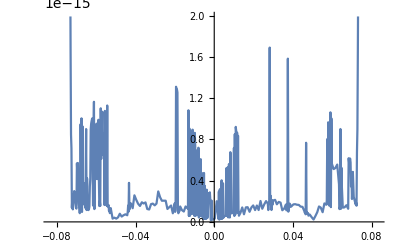

```mathematica
Plot[Norm[Transpose[snsFilledIn[{Subscript[k, x]->phi,Ez->.15,θ->0, α->60,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200}~Join~units]]+
snsFilledIn[{Subscript[k, x]->-phi,Ez->-.15,θ->0, α->60,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200}~Join~units]],{phi,-0.08324525,0.08300824525}, PlotPoints->180, MaxRecursion->2]
```

# Test sns matrix

```mathematica
units={ℏ->6.582119514467406*10^(-13),Subscript[m, s]->1.1371260124182183*10^(-28)};
```

```mathematica
ksFilledIn[pars_]:={subK1/.pars,subK2/.pars,subQ/.pars};
```

```mathematica
ksMinFilledIn[pars_]:={subK1/.(Subscript[k, x]->-Subscript[k, x])/.pars,subK2/.(Subscript[k, x]->-Subscript[k, x])/.pars,subQ/.(Subscript[k, x]->-Subscript[k, x])/.pars}
```

```mathematica
subGamFilledIn[pars_]:=subGamma/.ksFilledIn[pars]/.pars
```

```mathematica
subGamMinFilledIn[pars_]:=subGamma/.{Subscript[k, x]->-Subscript[k, x]}/.ksMinFilledIn[pars]/.pars
```

```mathematica
subOmegaFilledIn[pars_]:=subOmega/.subGamFilledIn[pars]
```

```mathematica
subOmegaMinFilledIn[pars_]:=subOmega/.subGamMinFilledIn[pars]
```

```mathematica
nuArgFilledIn[pars_] :=nuArg/.pars
```

```mathematica
nuArgMinFilledIn[pars_] :=nuArg/.(Subscript[ν, arg]->Subscript[ν, argm])/.(Subscript[k, x]->-Subscript[k, x])/.pars
```

```mathematica
snsFilledIn[pars_]:=Ssns/.nuArgFilledIn[pars]/.subOmegaFilledIn[pars]/.pars/.ksFilledIn[pars]
```

```mathematica
snsMinKFilledIn[pars_]:=(Ssns/.(Subscript[ν, arg]->Subscript[ν, argm]))/.nuArgMinFilledIn[pars]/.subOmegaMinFilledIn[pars]/.pars/.ksMinFilledIn[pars]
```

```mathematica
temp=snsFilledIn[{Subscript[k, x]->0.0000001,Ez->0.0000000,θ->0*Pi/4, α->20,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200}~Join~units]
```

{{3.24655×10^-8-8.80262×10^-8 ⅈ,1.03015×10^-13-1.06942×10^-13 ⅈ,-1.44905×10^-6+5.0103×10^-17 ⅈ,1.-7.52731×10^-14 ⅈ},{-1.03015×10^-13+1.06942×10^-13 ⅈ,3.24655×10^-8-8.80262×10^-8 ⅈ,-1.+7.52731×10^-14 ⅈ,-1.44905×10^-6+5.01057×10^-17 ⅈ},{-1.44905×10^-6+5.0103×10^-17 ⅈ,1.-7.52731×10^-14 ⅈ,3.24655×10^-8+8.80262×10^-8 ⅈ,-8.90661×10^-15+1.48221×10^-13 ⅈ},{-1.+7.52731×10^-14 ⅈ,-1.44905×10^-6+5.01057×10^-17 ⅈ,8.90661×10^-15-1.48221×10^-13 ⅈ,3.24655×10^-8+8.80262×10^-8 ⅈ}}

```mathematica
Chop[Simplify[temp+Transpose[temp]]]//MatrixForm
```

(6.4931×10^-8-1.76052×10^-7 ⅈ | 0 | -2.8981×10^-6 | 0
0 | 6.4931×10^-8-1.76052×10^-7 ⅈ | 0 | -2.8981×10^-6
-2.8981×10^-6 | 0 | 6.4931×10^-8+1.76052×10^-7 ⅈ | 0
0 | -2.8981×10^-6 | 0 | 6.4931×10^-8+1.76052×10^-7 ⅈ)

```mathematica
snsFilledIn[{Subscript[k, x]->0.01,Ez->2,θ->0*Pi/4, α->20,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200}~Join~units].Conjugate[snsFilledIn[{Subscript[k, x]->-0.01,Ez->2,θ->0*Pi/4, α->20,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200}~Join~units]]//MatrixForm
```

(0.962805-0.19628 ⅈ | -3.46945×10^-18-0.184393 ⅈ | -0.000465956+0.00403446 ⅈ | -0.0210367-0.00458626 ⅈ
1.73472×10^-18-0.184393 ⅈ | 0.962805+0.19628 ⅈ | -0.0210367-0.00458626 ⅈ | -0.00125563+0.00386231 ⅈ
-0.00125563-0.00386231 ⅈ | 0.0210367-0.00458626 ⅈ | 0.962805-0.19628 ⅈ | -3.46945×10^-18-0.184393 ⅈ
0.0210367-0.00458626 ⅈ | -0.000465956-0.00403446 ⅈ | 1.68051×10^-18-0.184393 ⅈ | 0.962805+0.19628 ⅈ)

# Solve ABS problem

```mathematica
rAFilledIn[pars_]:={{Exp[-I ϕ/2],0,0,0},{0,Exp[-I ϕ/2],0,0},{0,0,Exp[I ϕ/2],0},{0,0,0,Exp[I ϕ/2]}}/.pars;rAFilledIn[{}]//MatrixForm
```

(ⅇ^(-(ⅈ ϕ)/2) | 0 | 0 | 0
0 | ⅇ^(-(ⅈ ϕ)/2) | 0 | 0
0 | 0 | ⅇ^((ⅈ ϕ)/2) | 0
0 | 0 | 0 | ⅇ^((ⅈ ϕ)/2))

```mathematica
eq1[pars_]:=rAFilledIn[pars].Conjugate[snsMinKFilledIn[pars]].Conjugate[rAFilledIn[pars]].snsFilledIn[pars]
```

```mathematica
eq2[pars_]:=-Eigenvalues[eq1[pars]]
```

```mathematica
eq3[pars_]:=Select[(Α~Join~(-Α))/.Α->Sqrt[1/eq2[pars]],Im[#] <=0&]
```

```mathematica
eq4[pars_]:=Sort[Re[(1+Α^2)/(2 Α)]/.Α->eq3[pars]]
```

```mathematica
eq4[{Subscript[k, x]->0.07,Ez->1.5*1,θ->ArcTan[1/2], α->20,Subscript[μ, n]->10,Subscript[μ, s]->10, W->80,ϕ->Pi}~Join~units]
```

{-0.999717,-0.222779,0.576909,0.990612}

```mathematica
La[zx_,zy_,W_]:=Sqrt[zx^2/4+(2*zy)^2]+W;
```

```mathematica
KX[zx_,zy_,W_]:=La[zx,zy,W]/Sqrt[La[zx,zy,W]^2+W^2];
```

```mathematica
.229*KX[800,200,200]//N
```

0.221566

```mathematica
0.07245252598530769*KX[800,200,800]//N
```

0.0625161

```mathematica
(Sqrt[200^2+800^2]+150)/Sqrt[(Sqrt[200^2+800^2]+150)^2 +150^2]*0.07245252598530769//N
```

0.0716094

```mathematica
Sqrt[100*Subscript[m, s]*2]/ℏ/.units
```

0.229115

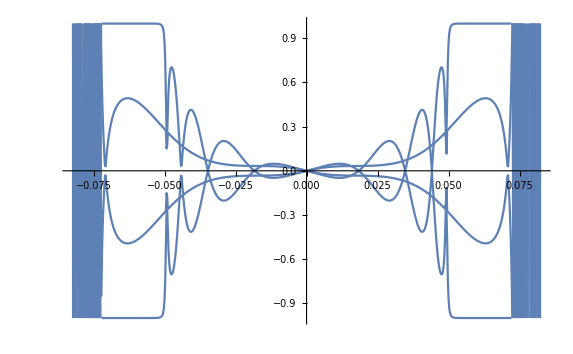

```mathematica
Plot[eq4[{Subscript[k, x]->phi,Ez->0,θ->0, α->100,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200, ϕ->Pi}~Join~units],{phi,-0.0824525,0.0824525}, PlotPoints->180, MaxRecursion->2, PlotRange->{-1,1}]
```

```mathematica
√(Ez^2-2 Ez α Sin[θ] Subscript[k, x]+α^2 Subscript[k, x]^2)/.({Subscript[k, x]->0.018,Ez->0,θ->0, α->100,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200, ϕ->Pi}~Join~units)
```

1.8

```mathematica
Solve[Subscript[ϵ, 1,n]==0,Subscript[k, y]]/.({Subscript[k, x]->0.018,Ez->0,θ->0, α->100,Subscript[μ, n]->10,Subscript[μ, s]->10, W->200, ϕ->Pi}~Join~units)
```

{{k_y→-0.0630911},{k_y→0.0630911}}

```mathematica
temp=Table[{phi,eq4[{Subscript[k, x]->phi,Ez->1.5,θ->0*ArcTan[0], α->20,Subscript[μ, n]->100,Subscript[μ, s]->100, W->200, ϕ->Pi}~Join~units][[1]]},{phi,-0.2,.2, .01}];
```

```mathematica
tempx=Table[phi, {phi,-0.2,.2, .001}];
```

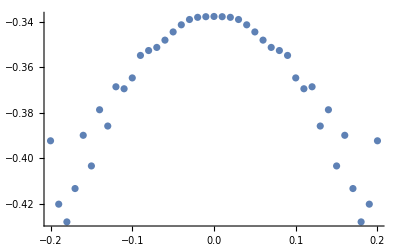

```mathematica
ListPlot[temp]
```

```mathematica
Simplify[snsFilledIn[{ℏ->1, Subscript[m, s]->2, W->100, Ez->1, θ->0, Subscript[μ, n]->10, Subscript[μ, s]->10, α->20}]]//MatrixForm
```

$Aborted

```mathematica
sns
```